```mathematica
FermiDirac[ϵ_,β_]:= 1/(Exp[β*ϵ]+1)
```

```mathematica
Lor[ϵ_,Γ_,ϵ0_]:= Γ/( (ϵ-ϵ0)^2 +(Γ^2/4) )
```

```mathematica
Lor[ϵ,Γ,a]
```

Γ/(Γ^2/4+(-a+ϵ)^2)

```mathematica
F[ϵ_,β_,ω0_,Γr_,Γl_,ϵa_,ϵd_]:= Exp[β*(ϵ-ω0)]*FermiDirac[ϵ,β]*FermiDirac[ϵ-ω0,β]*Lor[ϵ-ω0,Γr,ϵa]*Lor[ϵ,Γl,ϵd]
```

```mathematica
F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd]
```

(ⅇ^(β (ϵ-ω0)) Γl Γr)/((1+ⅇ^(β ϵ)) (1+ⅇ^(β (ϵ-ω0))) (Γl^2/4+(ϵ-ϵd)^2) (Γr^2/4+(ϵ-ϵa-ω0)^2))

```mathematica
Integrate[F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd],{ϵ,-Infinity,Infinity}]
```

$Aborted

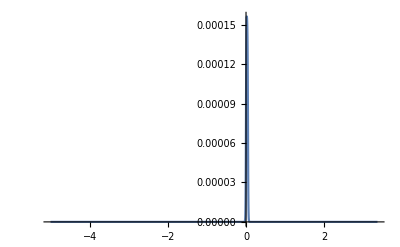

```mathematica
Plot[F[ϵ,200,0.05,0.2,0.2,0.4,-0.2],{ϵ,-5,5},PlotRange->All]
```

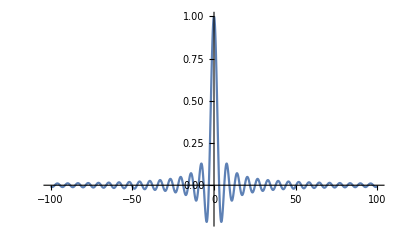

```mathematica
Plot[Sin[ϵ]/ϵ,{ϵ,-100,100},PlotRange->All]
```

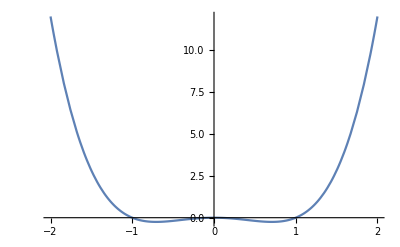

```mathematica
Plot[x^4 - x^2,{x,-2,2}]
```

```mathematica
Assuming[n∈Integers,Residue[F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd],{ϵ,(2*n+1)*ⅈ*π/β}]]
```

-((16 β^3 Γl Γr)/((ⅇ^(2 ⅈ n π)-ⅇ^(β ω0)) (-4 π^2-16 n π^2-16 n^2 π^2+β^2 Γl^2-8 ⅈ π β ϵd-16 ⅈ n π β ϵd+4 β^2 ϵd^2) (-4 π^2-16 n π^2-16 n^2 π^2+β^2 Γr^2-8 ⅈ π β ϵa-16 ⅈ n π β ϵa+4 β^2 ϵa^2-8 ⅈ π β ω0-16 ⅈ n π β ω0+8 β^2 ϵa ω0+4 β^2 ω0^2)))

```mathematica
Assuming[{β>0, ω0>0,Γl>0, Γr>0, ϵa∈Reals,ϵd∈Reals}, ∑_(n=1)^∞ %4]
```

-((2 (Γl^2 Γr PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]-Γr^3 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]+4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]-4 Γr ϵa^2 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]-4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]+8 Γr ϵa ϵd PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]-4 Γr ϵd^2 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]+4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]-8 Γr ϵa ω0 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]+8 Γr ϵd ω0 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]-4 Γr ω0^2 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd)/(4 π)]-Γl^2 Γr PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]+Γr^3 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]+4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]+4 Γr ϵa^2 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]-4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]-8 Γr ϵa ϵd PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]+4 Γr ϵd^2 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]+4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]+8 Γr ϵa ω0 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]-8 Γr ϵd ω0 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]+4 Γr ω0^2 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd)/(4 π)]-Γl^3 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+Γl Γr^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-4 Γl ϵa^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+8 Γl ϵa ϵd PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-4 Γl ϵd^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-8 Γl ϵa ω0 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+8 Γl ϵd ω0 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-4 Γl ω0^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+Γl^3 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-Γl Γr^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+4 Γl ϵa^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-8 Γl ϵa ϵd PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+4 Γl ϵd^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+8 Γl ϵa ω0 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]-8 Γl ϵd ω0 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]+4 Γl ω0^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa-2 ⅈ β ω0)/(4 π)]))/((1-ⅇ^(β ω0)) π (Γl-Γr-2 ⅈ ϵa+2 ⅈ ϵd-2 ⅈ ω0) (Γl+Γr-2 ⅈ ϵa+2 ⅈ ϵd-2 ⅈ ω0) (Γl-Γr+2 ⅈ ϵa-2 ⅈ ϵd+2 ⅈ ω0) (Γl+Γr+2 ⅈ ϵa-2 ⅈ ϵd+2 ⅈ ω0)))

```mathematica
FullSimplify[%5]
```

```mathematica
1/((-1+ⅇ^(β ω0)) π)2 ((Γr HarmonicNumber[(2 π-β Γl+2 ⅈ β ϵd)/(4 π)])/((-Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γr HarmonicNumber[(2 π+β Γl+2 ⅈ β ϵd)/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (-Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(Γl HarmonicNumber[(2 π+β (-Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl-Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γl HarmonicNumber[(2 π+β (Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl-Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0))))
```

```mathematica
Assuming[n∈Integers,Residue[F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd],{ϵ,ω0+(2*n+1)*ⅈ*π/β}]]
```

-(16 β^3 Γl Γr)/((-1+ⅇ^(2 ⅈ n π+β ω0)) (-4 π^2-16 n π^2-16 n^2 π^2+β^2 Γr^2-8 ⅈ π β ϵa-16 ⅈ n π β ϵa+4 β^2 ϵa^2) (-4 π^2-16 n π^2-16 n^2 π^2+β^2 Γl^2-8 ⅈ π β ϵd-16 ⅈ n π β ϵd+4 β^2 ϵd^2+8 ⅈ π β ω0+16 ⅈ n π β ω0-8 β^2 ϵd ω0+4 β^2 ω0^2))

```mathematica
Assuming[{β>0, ω0>0,Γl>0, Γr>0, ϵa∈Reals,ϵd∈Reals}, ∑_(n=1)^∞ %8]
```

(2 (Γl^3 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]-Γl Γr^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]+4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]+4 Γl ϵa^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]-4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]-8 Γl ϵa ϵd PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]+4 Γl ϵd^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]+4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]+8 Γl ϵa ω0 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]-8 Γl ϵd ω0 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]+4 Γl ω0^2 PolyGamma[0,-(-6 π-β Γr-2 ⅈ β ϵa)/(4 π)]-Γl^3 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]+Γl Γr^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]+4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]-4 Γl ϵa^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]-4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]+8 Γl ϵa ϵd PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]-4 Γl ϵd^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]+4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]-8 Γl ϵa ω0 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]+8 Γl ϵd ω0 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]-4 Γl ω0^2 PolyGamma[0,-(-6 π+β Γr-2 ⅈ β ϵa)/(4 π)]-Γl^2 Γr PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+Γr^3 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+4 Γr ϵa^2 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-8 Γr ϵa ϵd PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+4 Γr ϵd^2 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+8 Γr ϵa ω0 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-8 Γr ϵd ω0 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+4 Γr ω0^2 PolyGamma[0,-(-6 π-β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+Γl^2 Γr PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-Γr^3 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ϵa PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-4 Γr ϵa^2 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+4 ⅈ Γl Γr ϵd PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+8 Γr ϵa ϵd PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-4 Γr ϵd^2 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-4 ⅈ Γl Γr ω0 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-8 Γr ϵa ω0 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]+8 Γr ϵd ω0 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]-4 Γr ω0^2 PolyGamma[0,-(-6 π+β Γl-2 ⅈ β ϵd+2 ⅈ β ω0)/(4 π)]))/((-1+ⅇ^(β ω0)) π (-ⅈ Γl-ⅈ Γr+2 ϵa-2 ϵd+2 ω0) (ⅈ Γl-ⅈ Γr+2 ϵa-2 ϵd+2 ω0) (-ⅈ Γl+ⅈ Γr+2 ϵa-2 ϵd+2 ω0) (ⅈ Γl+ⅈ Γr+2 ϵa-2 ϵd+2 ω0))

```mathematica
Simplify[%10]
```

(2 ⅈ (-Γl (Γl^2-(Γr+2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π-β Γr+2 ⅈ β ϵa)/(4 π)]+Γl (Γl^2-(Γr-2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π+β Γr+2 ⅈ β ϵa)/(4 π)]+Γr ((Γl^2-Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)-4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π-β (Γl-2 ⅈ (ϵd-ω0)))/(4 π)]+(-Γl^2+Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)+4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π+β (Γl+2 ⅈ (ϵd-ω0)))/(4 π)])))/((-1+ⅇ^(β ω0)) π (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)) (ⅈ Γl-ⅈ Γr+2 (ϵa-ϵd+ω0)) (-ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)) (ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)))

```mathematica
%11 + %6
```

(2 ((Γr HarmonicNumber[(2 π-β Γl+2 ⅈ β ϵd)/(4 π)])/((-Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γr HarmonicNumber[(2 π+β Γl+2 ⅈ β ϵd)/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (-Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(Γl HarmonicNumber[(2 π+β (-Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl-Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γl HarmonicNumber[(2 π+β (Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl-Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))))/((-1+ⅇ^(β ω0)) π)+(2 ⅈ (-Γl (Γl^2-(Γr+2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π-β Γr+2 ⅈ β ϵa)/(4 π)]+Γl (Γl^2-(Γr-2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π+β Γr+2 ⅈ β ϵa)/(4 π)]+Γr ((Γl^2-Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)-4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π-β (Γl-2 ⅈ (ϵd-ω0)))/(4 π)]+(-Γl^2+Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)+4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π+β (Γl+2 ⅈ (ϵd-ω0)))/(4 π)])))/((-1+ⅇ^(β ω0)) π (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)) (ⅈ Γl-ⅈ Γr+2 (ϵa-ϵd+ω0)) (-ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)) (ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)))

```mathematica
Assuming[{β>0, ω0>0,Γl>0, Γr>0, ϵa∈Reals,ϵd∈Reals},Simplify[%12]]
```

1/((-1+ⅇ^(β ω0)) π)2 ((Γr HarmonicNumber[(2 π-β Γl+2 ⅈ β ϵd)/(4 π)])/((-Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γr HarmonicNumber[(2 π+β Γl+2 ⅈ β ϵd)/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (-Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(Γl HarmonicNumber[(2 π+β (-Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl-Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γl HarmonicNumber[(2 π+β (Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl-Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(ⅈ (-Γl (Γl^2-(Γr+2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π-β Γr+2 ⅈ β ϵa)/(4 π)]+Γl (Γl^2-(Γr-2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π+β Γr+2 ⅈ β ϵa)/(4 π)]+Γr ((Γl^2-Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)-4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π-β (Γl-2 ⅈ (ϵd-ω0)))/(4 π)]+(-Γl^2+Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)+4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π+β (Γl+2 ⅈ (ϵd-ω0)))/(4 π)])))/((Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)) (ⅈ Γl-ⅈ Γr+2 (ϵa-ϵd+ω0)) (-ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)) (ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0))))

```mathematica
Series[%13,{β,0,4}]
```

(ⅈ Γl Γr PolyGamma[4,3/2] β^3)/(192 π^5)+((3840 Γl Γr ϵa-4 π^6 Γl Γr ϵa+3840 Γl Γr ϵd-4 π^6 Γl Γr ϵd-ⅈ π Γl Γr ω0 PolyGamma[4,3/2]) β^4)/(384 π^6)+O[β]^5

Series[1/((-1+ⅇ^(β ω0)) π)2 ((Γr HarmonicNumber[(2 π-β Γl+2 ⅈ β ϵd)/(4 π)])/((-Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γr HarmonicNumber[(2 π+β Γl+2 ⅈ β ϵd)/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (-Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(Γl HarmonicNumber[(2 π+β (-Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl-Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γl HarmonicNumber[(2 π+β (Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl-Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(ⅈ (-Γl (Γl^2-(Γr+2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π-β Γr+2 ⅈ β ϵa)/(4 π)]+Γl (Γl^2-(Γr-2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π+β Γr+2 ⅈ β ϵa)/(4 π)]+Γr ((Γl^2-Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)-4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π-β (Γl-2 ⅈ (ϵd-ω0)))/(4 π)]+(-Γl^2+Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)+4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π+β (Γl+2 ⅈ (ϵd-ω0)))/(4 π)])))/((Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)) (ⅈ Γl-ⅈ Γr+2 (ϵa-ϵd+ω0)) (-ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)) (ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)))),{1/β,0,4}]

```mathematica
Residue[F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd],{ϵ,(3*ⅈ*π/β)+ω0}]
```

-((16 β^3 Γl Γr)/((-1+ⅇ^(β ω0)) (-36 π^2+β^2 Γr^2-24 ⅈ π β ϵa+4 β^2 ϵa^2) (-36 π^2+β^2 Γl^2-24 ⅈ π β ϵd+4 β^2 ϵd^2+24 ⅈ π β ω0-8 β^2 ϵd ω0+4 β^2 ω0^2)))

```mathematica
Residue[F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd],{ϵ,(ⅈ*π/β)+ω0}]
```

-(16 β^3 Γl Γr)/((-1+ⅇ^(β ω0)) (-4 π^2+β^2 Γr^2-8 ⅈ π β ϵa+4 β^2 ϵa^2) (-4 π^2+β^2 Γl^2-8 ⅈ π β ϵd+4 β^2 ϵd^2+8 ⅈ π β ω0-8 β^2 ϵd ω0+4 β^2 ω0^2))

```mathematica
Residue[F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd],{ϵ,(ⅈ*π/β)}]
```

(16 β^3 Γl Γr)/((-1+ⅇ^(β ω0)) (-4 π^2+β^2 Γl^2-8 ⅈ π β ϵd+4 β^2 ϵd^2) (-4 π^2+β^2 Γr^2-8 ⅈ π β ϵa+4 β^2 ϵa^2-8 ⅈ π β ω0+8 β^2 ϵa ω0+4 β^2 ω0^2))

```mathematica
Residue[F[ϵ,β,ω0,Γr,Γl,ϵa,ϵd],{ϵ,(3*ⅈ*π/β)}]
```

(16 β^3 Γl Γr)/((-1+ⅇ^(β ω0)) (-36 π^2+β^2 Γl^2-24 ⅈ π β ϵd+4 β^2 ϵd^2) (-36 π^2+β^2 Γr^2-24 ⅈ π β ϵa+4 β^2 ϵa^2-24 ⅈ π β ω0+8 β^2 ϵa ω0+4 β^2 ω0^2))

```mathematica
Limit[%17,{β-> Infinity}]
```

{Limit[1/((-1+ⅇ^(β ω0)) π)2 ((Γr HarmonicNumber[(2 π-β Γl+2 ⅈ β ϵd)/(4 π)])/((-Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γr HarmonicNumber[(2 π+β Γl+2 ⅈ β ϵd)/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (-Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(Γl HarmonicNumber[(2 π+β (-Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl+Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl-Γr+2 ⅈ (ϵa-ϵd+ω0)))-(Γl HarmonicNumber[(2 π+β (Γr+2 ⅈ (ϵa+ω0)))/(4 π)])/((Γl-Γr-2 ⅈ (ϵa-ϵd+ω0)) (Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)))+(ⅈ (-Γl (Γl^2-(Γr+2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π-β Γr+2 ⅈ β ϵa)/(4 π)]+Γl (Γl^2-(Γr-2 ⅈ (ϵa-ϵd+ω0))^2) PolyGamma[0,(6 π+β Γr+2 ⅈ β ϵa)/(4 π)]+Γr ((Γl^2-Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)-4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π-β (Γl-2 ⅈ (ϵd-ω0)))/(4 π)]+(-Γl^2+Γr^2-4 ⅈ Γl (ϵa-ϵd+ω0)+4 (ϵa-ϵd+ω0)^2) PolyGamma[0,(6 π+β (Γl+2 ⅈ (ϵd-ω0)))/(4 π)])))/((Γl+Γr+2 ⅈ (ϵa-ϵd+ω0)) (ⅈ Γl-ⅈ Γr+2 (ϵa-ϵd+ω0)) (-ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)) (ⅈ Γl+ⅈ Γr+2 (ϵa-ϵd+ω0)))),β→∞]}

```mathematica
Limit[HarmonicNumber[(2 π-2β*Γl + 2 ⅈ β)/(4 π)],β-> Infinity]
```

Limit[HarmonicNumber[(2 π+2 ⅈ β-2 β Γl)/(4 π)],β→∞]

```mathematica
Integrate[Sin[x],{x,-Infinity,Infinity}]
```

Integrate::idiv: Integral of Sin[x] does not converge on {-∞,∞}.

∫_(-∞)^∞ Sin[x]ⅆx